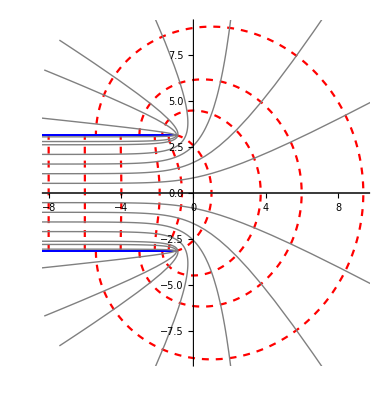

```mathematica
Potential=ParametricPlot[{{u+Exp[u] Cos[Pi / 6],Pi / 6+Exp[u]Sin[Pi / 6]},{u+Exp[u],0},{u+Exp[u] Cos[Pi / 3],Pi / 3+Exp[u] Sin[Pi / 3]},{u+Exp[u] Cos[Pi / 2],Pi / 2+Exp[u] Sin[Pi / 2]},{u+Exp[u] Cos[2 Pi / 3],2 Pi / 3+Exp[u] Sin[2 Pi / 3]},{u+Exp[u] Cos[5 Pi / 6],5 Pi / 6+Exp[u] Sin[5 Pi / 6]},{u+Exp[u] Cos[8 Pi / 9],8 Pi / 9+Exp[u] Sin[8 Pi / 9]},{u+Exp[u] Cos[0.97Pi],0.97Pi+Exp[u] Sin[0.97Pi]},
{u+Exp[u] Cos[-Pi / 6],-Pi / 6+Exp[u]Sin[-Pi / 6]},{u+Exp[u],0},{u+Exp[u] Cos[-Pi / 3],-Pi / 3+Exp[u] Sin[-Pi / 3]},{u+Exp[u] Cos[-Pi / 2],-Pi / 2+Exp[u] Sin[-Pi / 2]},{u+Exp[u] Cos[-2 Pi / 3],-2 Pi / 3+Exp[u] Sin[-2 Pi / 3]},{u+Exp[u] Cos[-5 Pi / 6],-5 Pi / 6+Exp[u] Sin[-5 Pi / 6]},{u+Exp[u] Cos[-8 Pi / 9],-8 Pi / 9+Exp[u] Sin[-8 Pi / 9]},{u+Exp[u] Cos[-0.97Pi],-0.97Pi+Exp[u] Sin[-0.97Pi]}},{u,-9,2.43},PlotStyle->{{Gray,Thick},{Gray,Thick}}];
Plates=ParametricPlot[{{u+Exp[u] Cos[Pi],Pi+Exp[u] Sin[Pi]},{u+Exp[u] Cos[-Pi],-Pi+Exp[u] Sin[-Pi]}},{u,-9,2.43},PlotStyle->{{Blue,Thick},{Blue,Thick}}];
Electric=ParametricPlot[{{-8.+Exp[-8] Cos[v],v+Exp[-8] Sin[v]},{-6.+Exp[-6] Cos[v],v+Exp[-6] Sin[v]},{-4+Exp[-4] Cos[v],v+Exp[-4] Sin[v]},{-2+Exp[-2] Cos[v],v+Exp[-2] Sin[v]},{-1+Exp[-1] Cos[v],v+Exp[-1] Sin[v]},{0+Exp[0] Cos[v],v+Exp[0] Sin[v]},{1+Exp[1] Cos[v],v+Exp[1] Sin[v]},{2+Exp[2] Cos[v],v+Exp[2] Sin[v]},{1.5+Exp[1.5] Cos[v],v+Exp[1.5] Sin[v]}},{v,-π,Pi},PlotStyle->{{Red,Dashed},{Red,Dashed}}];
Show[Electric,Plates,Potential]
```

```mathematica
aa=1+(4*I*w)/(1-2*I*w+w^2)//FullSimplify
((1+2*I*zz+zz^2))/(1-2*I*zz+zz^2)//FullSimplify
```

1+(4 ⅈ w)/(1+w (-2 ⅈ+w))

(ⅇ^(2 ⅈ x) (a-z)^2-2 ⅈ ⅇ^(ⅈ x) (a-z) (-1+ba z)+(-1+ba z)^2)/(ⅇ^(2 ⅈ x) (a-z)^2+2 ⅈ ⅇ^(ⅈ x) (a-z) (-1+ba z)+(-1+ba z)^2)

```mathematica
(ⅇ^(ⅈ x) (-a+aa))/(-1+ba aa)
```

(ⅇ^(ⅈ x) (1-a+(4 ⅈ w)/(1+w (-2 ⅈ+w))))/(-1+ba (1+(4 ⅈ w)/(1+w (-2 ⅈ+w))))

```mathematica
FullSimplify[(ⅇ^(ⅈ x) (1-a+(4 ⅈ w)/(1+w (-2 ⅈ+w))))/(-1+ba (1+(4 ⅈ w)/(1+w (-2 ⅈ+w))))]
```

(ⅇ^(ⅈ x) (1+w (2 ⅈ+w)-a (1+w (-2 ⅈ+w))))/(-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2)

```mathematica
Simplify[(4 ⅈ ⅇ^(ⅈ x) (-a+z))/((-1+ba z) (1+(ⅇ^(2 ⅈ x) (-a+z)^2)/(-1+ba z)^2-(2 ⅈ ⅇ^(ⅈ x) (-a+z))/(-1+ba z)))]
```

```mathematica
(4 ⅈ ⅇ^(ⅈ x) (-a+z))/((-1+ba z) (1+(ⅇ^(2 ⅈ x) (a-z)^2)/(-1+ba z)^2+(2 ⅈ ⅇ^(ⅈ x) (a-z))/(-1+ba z)))//FullSimplify
```

4/(-2+(ⅈ ⅇ^(ⅈ x) (a-z))/(-1+ba z)+((-1+ba z) (ⅈ Cos[x]+Sin[x]))/(a-z))

```mathematica
-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2
```

```mathematica
-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2//FullSimplify
```

-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2

```mathematica
Factor[-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2]
```

```mathematica
-1+ba+2 ⅈ w+2 ⅈ ba w-w^2+ba w^2==ba(w^2+2I w+1 )-w^2+2I w-1
```

-1+ba+2 ⅈ w+2 ⅈ ba w-w^2+ba w^2==-1+2 ⅈ w-w^2+ba (1+2 ⅈ w+w^2)

```mathematica
FindInstance[-1+ba+2 ⅈ w+2 ⅈ ba w-w^2+ba w^2==-1+2 ⅈ w-w^2+ba (1+2 ⅈ w+w^2),{ba,w}]
```

{{ba→0,w→0}}

```mathematica
-1+ba+2 ⅈ (1+ba) w+(-1+ba) w^2//Expand
```

```mathematica
Collect[-1+ba+2 ⅈ w+2 ⅈ ba w-w^2+ba w^2,ba]
```

-1+2 ⅈ w-w^2+ba (1+2 ⅈ w+w^2)

```mathematica
G1 = Annulus[{0,0},{3.95,4}];
G2 =Annulus[{0,1.5},{1.45,1.5}];
G3 = Annulus[{12,0},{3.95,4}];
G4 =Annulus[{12,0},{1.45,1.5}];
G5 = Arrow[{{5,0},{7,0}}]
Graphics[{G1,G2,G3,G4,G5}]
```

Arrow[{{5,0},{7,0}}]

-Graphics-

```mathematica
Annulus[{0,1.5},{1.45,1.5}]
```

Annulus[{0,1.5},{1.45,1.5}]